## Problems: Torque Control With a Swarm of Normally distributed Particles Under Global Control Given a swarm of particles, whose positions are normally distributed, and a pivoted object, where should the swarm hit to generate the maximum torque? related problem: shooting a railroad track switch with a shotgun. F = force provided by entire swarm N = number of particles F/N = force per particle ⅇ^(-(x-μ)^2/(2 σ^2))

### Problem 1: marginalizing to 1 dimension, not thinking about distributed time of impact this is only a one-pass of the swarm at the object. The kilobots are pushing continuously. (math is for one step, real world is an iterative process)

```mathematica
pdfNormal[x_,μ_,σ_]:=1/(√(2 π) σ) ⅇ^(-(x-μ)^2/(2 σ^2))
```

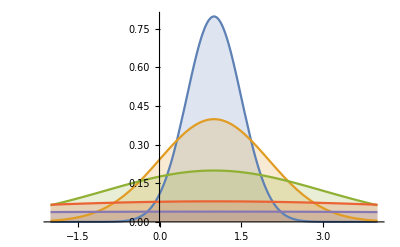

```mathematica
Plot[Evaluate[pdfNormal[x,1,σ]/.σ->{1/2,1,2,5,10}],{x,-2,4},Filling->Axis,PlotRange->All]
```

```mathematica
FullSimplify[∫_0^1 x pdfNormal[x,μ,σ]ⅆx] (*x is the moment arm, we integrate over the length of the object*)
```

((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])

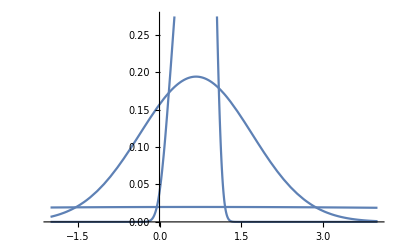
{0.21005,-Graphics-}

```mathematica
Timing[Plot[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])/.σ->{1/10,1,10},{μ,-2,4}]]
```

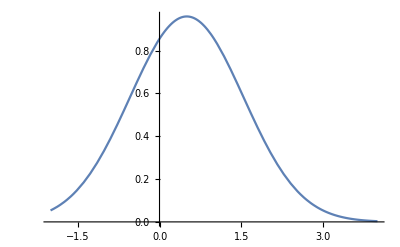
{4.13768,-Graphics-}

```mathematica
Timing[Plot[∫_0^1 pdfNormal[x,μ,1]ⅆx,{μ,-2,4}]]
```

```mathematica
Torque[μ_,σ_]:=((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])
```

```mathematica
D[Torque[μ,σ],μ]
```

1/2 μ (-(ⅇ^(-(1-μ)^2/(2 σ^2)) √(2/π))/σ+(ⅇ^(-μ^2/(2 σ^2)) √(2/π))/σ)+(((ⅇ^(-(-1+μ)^2/(2 σ^2)) (-1+μ))/σ^2-(ⅇ^(-μ^2/(2 σ^2)) μ)/σ^2) σ)/(√(2 π))+1/2 (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])

```mathematica
Solve[1/2 μ (-(ⅇ^(-(1-μ)^2/(2 σ^2)) √(2/π))/σ+(ⅇ^(-μ^2/(2 σ^2)) √(2/π))/σ)+(((ⅇ^(-(-1+μ)^2/(2 σ^2)) (-1+μ))/σ^2-(ⅇ^(-μ^2/(2 σ^2)) μ)/σ^2) σ)/(√(2 π))+1/2 (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])==0,{μ,σ}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/2 μ (-(ⅇ^(-(1-μ)^2/(2 σ^2)) √(2/π))/σ+(ⅇ^(-μ^2/(2 σ^2)) √(2/π))/σ)+(((ⅇ^(-(-1+μ)^2/(2 σ^2)) (-1+μ))/σ^2-(ⅇ^(-μ^2/(2 σ^2)) μ)/σ^2) σ)/(√(2 π))+1/2 (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])==0,{μ,σ}]

```mathematica
FindMaximum[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])/.σ->100,{μ,1}]
```

{0.00199471,{μ→0.666667}}

```mathematica
bestPush=Table[ans=FindMaximum[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]),{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

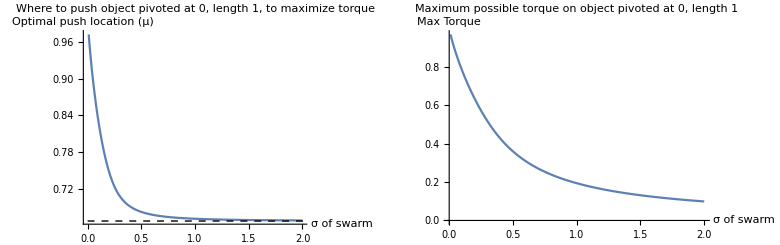

```mathematica
plotBestLocationPivotObject =ListPlot[{Transpose[{bestPush⟦;;,1⟧,bestPush⟦;;,3⟧}](*,
Transpose[{bestPush⟦;;,1⟧,2/3+1/3 ⅇ^(-6.5bestPush⟦;;,1⟧)}]*)},AxesLabel->{"σ of swarm","Optimal push location (μ)"},PlotRange->All,Joined->True,Epilog->{Dashed,Line[{{0,2/3},{100,2/3}}]},

Prolog-> Inset[pivotDrawing[1/10]],
PlotLabel->"Where to push object pivoted at 0, length 1, to maximize torque"];
plotMaxTorquePivotObject=ListPlot[Transpose[{bestPush⟦;;,1⟧,bestPush⟦;;,2⟧}],AxesLabel->{"σ of swarm","Max Torque"},Joined->True,PlotLabel->"Maximum possible torque on object pivoted at 0, length 1",ImageSize->Medium];
GraphicsRow[{plotBestLocationPivotObject,plotMaxTorquePivotObject}]
```

```mathematica
pivotDrawing[σ_]:=Graphics[{
Brown,
Rectangle[{0,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]},
PlotRange->{{-1,3},{-8,2}},AxesOrigin->{0,0}]
```

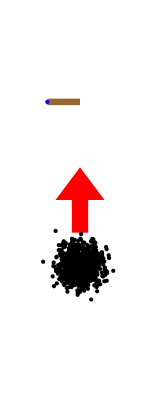
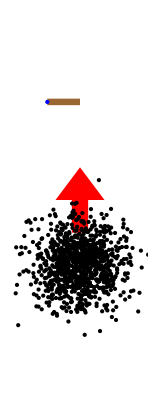
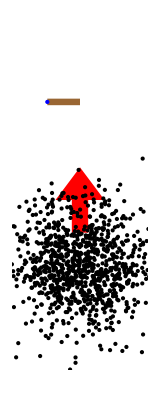
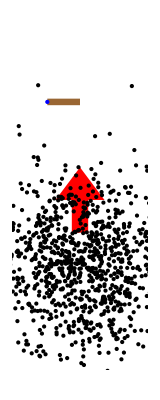

```mathematica
Table[Graphics[{
Brown,
Rectangle[{0,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]},
PlotRange->{{-1,3},{-8,2}},AxesOrigin->{0,0}],{σ,{1/10,1/2,1,2}}]
```

#### Trying to solve analytically is hard for me. Perhaps we can do this, but I’m not sure how so these used a numeric solution.

```mathematica
Maximize[(-ⅇ^(-1/2 (-1+μ)^2)+ⅇ^(-μ^2/2))/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2)]+Erf[μ/(√2)])/.σ-> 1,μ]
```

Maximize[(-ⅇ^(-1/2 (-1+μ)^2)+ⅇ^(-μ^2/2))/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2)]+Erf[μ/(√2)]),μ]

### Problem 2: a free object (no pivot point). Where should swarm fit to generate the most torque?

```mathematica
FullSimplify[∫_-1^1 x pdfNormal[x,μ,σ]ⅆx](*assume the object COM is at 0, and the object extends from -1 to 1*)
```

((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-(1+μ)^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[(1+μ)/(√2 σ)])

```mathematica
bestPushFree=Table[ans=FindMaximum[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-(1+μ)^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[(1+μ)/(√2 σ)]),{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

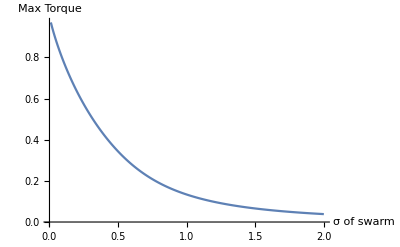

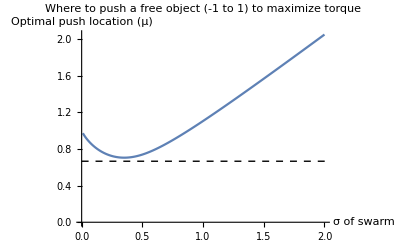

```mathematica
ListPlot[Transpose[{bestPushFree⟦;;,1⟧,bestPushFree⟦;;,2⟧}],AxesLabel->{"σ of swarm","Max Torque"},Joined->True]
ListPlot[{Transpose[{bestPushFree⟦;;,1⟧,bestPushFree⟦;;,3⟧}](*,
Transpose[{bestPush⟦;;,1⟧,2/3+1/3 ⅇ^(-6.5bestPush⟦;;,1⟧)}]*)},AxesLabel->{"σ of swarm","Optimal push location (μ)"},PlotRange->All,Joined->True,Epilog->{Dashed,Line[{{0,2/3},{100,2/3}}]},PlotLabel->"Where to push a free object (-1 to 1) to maximize torque"]
```

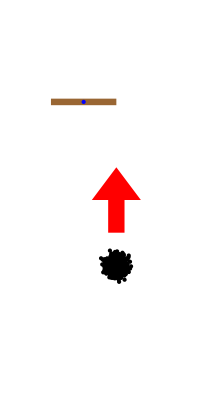
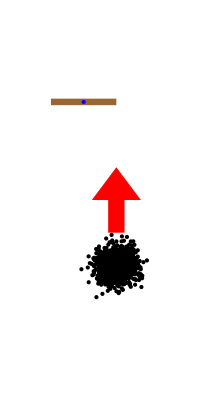
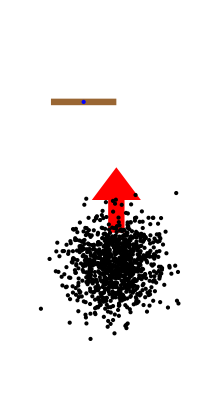
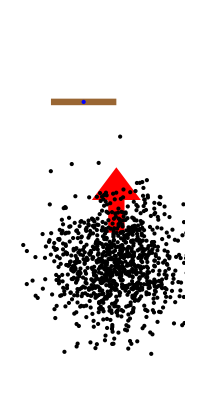
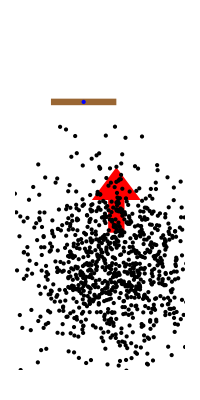

```mathematica
Table[Graphics[{
Brown,
Rectangle[{-1,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]
},
PlotRange->{{-2,3},{-8,2}},AxesOrigin->{0,0}],{σ,{1/50,1/10,1/2,1,2}}]
```

```mathematica
{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}
```

{{0.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{0.75,-3}}

### Problem 3: given a variance σ if you push at location μ, with velocity v (everyone not in contact with the object moves at velocity v) , and variance bound σ_max, how long before you need to switch to variance control mode?